## 1st Assignment: Stochastic FEM F. I. Giasemis

### B: Spectral representation method

#### Parameters

```mathematica
ωu=3; (* Cutoff frequency. *)
M=200; (* Number of terms in the expansion. *)
R=5000; (* Number of realizations. *)
```

#### Terms in the expansion

```mathematica
A[0]=0;
ω[0]=0;
Δω=ωu/M;
For[n=0,n<M-1,n=n+1;
ω[n]=n Δω;
If[ω[n]<1,
G[ω_]:=0;
A[n]=Sqrt[G[ω[n]] Δω];
]
If[1≤ω[n]≤2,
G[ω_]:=ω-1;
A[n]=Sqrt[G[ω[n]] Δω];
]
If[2<ω[n]≤3,
G[ω_]:=3-ω;
A[n]=Sqrt[G[ω[n]] Δω];
]
]
```

#### Random variables Φ

```mathematica
For[i=0,i<R,i=i+1;
Φ[i]=RandomVariate[UniformDistribution[{0,2Pi}],M-1]
]
```

#### Realization

```mathematica
Realization[i_,t_]:=Sqrt[2] Sum[A[n] Cos[ω[n] t+Φ[i][[n]]],{n,1,M-1}];
```

#### Example plot of a realization of X(t)

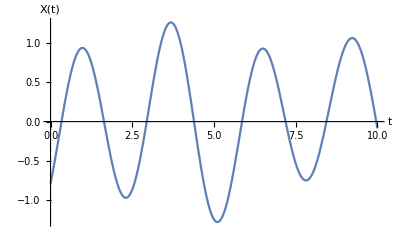

```mathematica
Plot[Realization[4578,t],{t,0,10},AxesLabel->{"t","X(t)"}]
```

#### Ensemble averages and variances

```mathematica
EnsembleAverage[t_]:=Mean[Table[Realization[i,t],{i,1,R}]]
EnsembleVariance[t_]:=Variance[Table[Realization[i,t],{i,1,R}]]
```

#### Example calculation of ensemble average and variance

```mathematica
EnsembleAverage[5]
EnsembleVariance[5]
```

0.00650853

0.986566

#### Temporal average and variance from a single realization

```mathematica
TempAverage[i_]:=NIntegrate[Realization[i,t],{t,0,10}]/10
TempVariance[i_]:=NIntegrate[Realization[i,t]^2,{t,0,10}]/10-(NIntegrate[Realization[i,t],{t,0,10}]/10)^2
```

#### Example calculation of temporal average and variance

```mathematica
TempAverage[4000]
TempVariance[4000]
```

-0.00159382

1.14668

#### Plot of 10 realizations

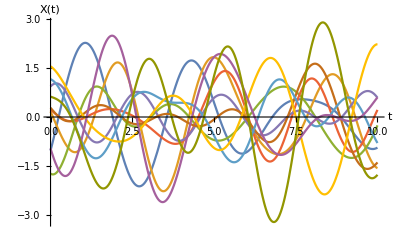

```mathematica
list={};
For[i=0,i<10,i=i+1;
AppendTo[list,Realization[i,t]]
]
Plot[list,{t,0,10},AxesLabel->{"t","X(t)"}]
```

#### Plot of 10 realizations

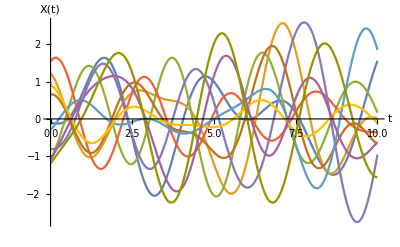

```mathematica
list={};
For[i=4100,i<4110,i=i+1;
AppendTo[list,Realization[i,t]]
]
Plot[list,{t,0,10},AxesLabel->{"t","X(t)"}]
```